```mathematica
Quit
```

## Solución de fondo

```mathematica
<<EDCRGTCcode.m
```

SetDelayed::write: Tag Classify in Classify[x_] is Protected.

```mathematica
Coord={t,r,θ,ϕ};
g={{-1,0,0,0},{0,a[t]^2,0,0},{0,0,a[t]^2r^2,0},{0,0,0,a[t]^2 r^2 Sin[θ]^2}};RGtensors[g,Coord]
```

gdd = (-1 | 0 | 0 | 0
0 | a[t]^2 | 0 | 0
0 | 0 | r^2 a[t]^2 | 0
0 | 0 | 0 | r^2 a[t]^2 Sin[θ]^2)

LineElement = a[t]^2 d[r]^2-d[t]^2+r^2 a[t]^2 d[θ]^2+r^2 a[t]^2 d[ϕ]^2 Sin[θ]^2

gUU = (-1 | 0 | 0 | 0
0 | 1/a[t]^2 | 0 | 0
0 | 0 | 1/(r^2 a[t]^2) | 0
0 | 0 | 0 | Csc[θ]^2/(r^2 a[t]^2))

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Conformally Flat

Einstein computed in 0. sec

All tasks completed in 0.03125 seconds

```mathematica
TUd={{-ρ[t],0,0,0},{0,p[t],0,0},{0,0,p[t],0},{0,0,0,p[t]}};
Tdd=Lower[TUd,1];
TdU=Raise[Tdd,2];
gUd=Raise[gdd,1];
RUd=Raise[Rdd,1];
```

```mathematica
f1 = k R; (*F=D[f,R]*)
F1=k;
f2=Exp[-(β f)/R^2]; (*β=H0^4*)
F2=(2 f β Exp[(-β f)/R^2])/(R)^3;
```

```mathematica
(*Variacion de la Accion respecto a la Metrica (Eq. 2 Paper)*)
EOM=Raise[(F1 - 2F2 ρ[t])Rdd-1/2 gdd f1 -covD[covD[F1-2F2 ρ[t]]]+gdd Tr[Raise[covD[covD[F1-2F2 ρ[t]]],1]]-f2 Tdd,1]//Simplify;
```

```mathematica
(*NO conservacion de Tmunu (Eq. 5 Paper)*)
TVar=(Contract[Raise[covD[Tdd],3],{2,3}]-F2/f2(-gdd ρ[t] - Tdd).Raise[covD[R],1]//Simplify)[[1]];
DSolve[TVar==0/.p[t]->ω ρ[t],ρ,t][[1,1,2,2,1]]//Simplify(*Ecuacion de la ρ[a[t]]*)
```

a[t]^(-3 (1+ω))

```mathematica
(*Cambios de a'[t]->a[t]H[t] y sus derivadas*)
Hubble[t_]:=D[a[t],t]/a[t]
HD1=D[Hubble[t],t]/. D[a[t],t]->H[t] a[t];
aD2=Solve[HD1==D[H[t],t],D[a[t],{t,2}]][[1,1]];
aDs={D[a[t],t]->H[t] a[t],aD2}; (*La lista que va a guardas las derivadas de a[t]*)
aD=Table[HD=D[Hubble[t],{t,i}]/. Join[{D[a[t],t]->H[t] a[t]},aDs];
sol=Solve[HD==D[H[t],{t,i}],D[a[t],{t,i+1}]][[1,1]];
AppendTo[aDs,sol];
sol,{i,2,3}];
(*Cambios H[t]->H[z] y Reglas de la Cadena*)
dzdt=-(z+1) H[z];
dHdt={dzdt D[H[z],z],0,0};
Table[
dHdt[[i]]=dzdt D [dHdt[[i-1]],z],{i,2,3}];
DHDt=Append[Table[Solve[D[H[t],{t,i}]==dHdt[[i]],D[H[t],{t,i}]],{i,1,3}],{H[t]->H[z],a[t]->1/(1+z)}]//Flatten ;(*Lista que me guarda los cambios*)
```

```mathematica
(*Insertamos estos cambios de variable en la Variación de la Métrica, además de una expansión Manual de H[z] para f y buscamos los valores para Hf0 y Hf1
Tomo los [[1,1]] porque el resto me depende de las derivadas o son las mismas ecuaciones*)
```

```mathematica
(*Orden cero*)
Series[EOM/.p->Function[t,-ρΛ ]/.ρ->Function[t,ρm  a[t]^(-3 (1))+ρΛ ]/.aDs/.DHDt/. H->Function[z,Hf0[z]+f β Hf1[z]+f^2/2 Hf2[z]],{f,0,0}][[1,1]]//Normal
```

ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ-3 k Hf0[z]^2

```mathematica
DSolve[(ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ-3 k Hf0[z]^2)==0,Hf0,z]
```

{{Hf0→Function[{z},-(√(ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ))/(√3 √k)]},{Hf0→Function[{z},(√(ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ))/(√3 √k)]}}

```mathematica
(*Orden 1*)
Series[EOM/.p->Function[t,-ρΛ ]/.ρ->Function[t,ρm  a[t]^(-3 (1))+ρΛ ]/.aDs/.DHDt/. H->Function[z,Hf0[z]+f β Hf1[z]+f^2/2 Hf2[z]]/.Hf0->Function[{z},(√(ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ))/(√3 √k)],{f,0,1}][[1,1]]//Simplify
```

(-((k^2 β ((1+z)^3 ρm+ρΛ) (-25 (1+z)^6 ρm^2+16 (1+z)^3 ρm ρΛ+32 ρΛ^2))/((1+z)^3 ρm+4 ρΛ)^4)-2 √3 √k β √((1+z)^3 ρm+ρΛ) Hf1[z]) f+O[f]^2

```mathematica
DSolve[(-((k^2 β ((1+z)^3 ρm+ρΛ) (-25 (1+z)^6 ρm^2+16 (1+z)^3 ρm ρΛ+32 ρΛ^2))/((1+z)^3 ρm+4 ρΛ)^4)-2 √3 √k β √((1+z)^3 ρm+ρΛ) Hf1[z]) f==0,Hf1,z]
```

{{Hf1→Function[{z},-((k^(3/2) √((1+z)^3 ρm+ρΛ) (-25 (1+z)^6 ρm^2+16 (1+z)^3 ρm ρΛ+32 ρΛ^2))/(2 √3 ((1+z)^3 ρm+4 ρΛ)^4))]}}

```mathematica
(*Finalmente verifico que sí sean soluciones*)
```

```mathematica
Series[EOM/.p->Function[t,-ρΛ ]/.ρ->Function[t,ρm  a[t]^(-3 (1))+ρΛ]/.aDs/.DHDt/. H->Function[z,Hf0[z]+f β Hf1[z]+f^2/2 Hf2[z]]/.Hf0->Function[{z},(√(ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ))/(√3 √k)]/.Hf1->Function[{z},-((k^(3/2) √((1+z)^3 ρm+ρΛ) (-25 (1+z)^6 ρm^2+16 (1+z)^3 ρm ρΛ+32 ρΛ^2))/(2 √3 ((1+z)^3 ρm+4 ρΛ)^4))],{f,0,1}]/.β->1//Simplify
```

{{O[f]^2,0,0,0},{0,O[f]^2,0,0},{0,0,O[f]^2,0},{0,0,0,O[f]^2}}

```mathematica
HZModel=Series[Hf0[z]+f β Hf1[z]/.Hf0->Function[z,(√(ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ))/(√3 √k)]/.Hf1->Function[{z},-((k^(3/2) √((1+z)^3 ρm+ρΛ) (-25 (1+z)^6 ρm^2+16 (1+z)^3 ρm ρΛ+32 ρΛ^2))/(2 √3 ((1+z)^3 ρm+4 ρΛ)^4))],{z,0,3}];
HzCosmo=H0(1+z(1+q0)+1/2 (-q0^2+j0)z^2);
```

```mathematica
(*Constriccion  de  Friedman con c=1, ya meto que β->H0^4*)
Simplify[Coefficient[HzCosmo,z,0]/H0==(Coefficient[HZModel,z,0]/H0/.ρΛ->3 H0^2 ΩΛ/(8 π G1)/.ρm->3 H0^2 Ωm/(8 π G1)/.k->1/(8 π G1)/.β->H0^4),{H0>0,G1>0}]
FriedmannCons=Coefficient[HZModel,z,0]/H0/.ρΛ->3 H0^2 ΩΛ/(8 π G1)/.ρm->3 H0^2 Ωm/(8 π G1)/.k->1/(8 π G1)/.β->H0^4;
```

1/18 √(Ωm+ΩΛ) (18+(f (25 Ωm^2-16 Ωm ΩΛ-32 ΩΛ^2))/(Ωm+4 ΩΛ)^4)==1

## Creación de las gráficas

```mathematica
G=6.67*10^-11;
κ=8 π G c^-4/.c->1;
Vars={ΩΛ,Ωm,f};
qs=Insert[Table[-(0.3+i/10),{i,0,6,2}],-0.53,2]; (*Valores para q*)
HZModel=Series[Hf0[z]+f β Hf1[z]/.Hf0->Function[z,(√(ρm+3 z ρm+3 z^2 ρm+z^3 ρm+ρΛ))/(√3 √k)]/.Hf1->Function[{z},-((k^(3/2) √((1+z)^3 ρm+ρΛ) (-25 (1+z)^6 ρm^2+16 (1+z)^3 ρm ρΛ+32 ρΛ^2))/(2 √3 ((1+z)^3 ρm+4 ρΛ)^4))],{z,0,3}];
HzCosmo=H0(1+z(1+q0)+1/2 (-q0^2+j0)z^2);
```

```mathematica
(*Solucion Central: Crea una solucion alrededor de un H0, q0, j0 específico.*)
ecuaciones=Table[Coefficient[HzCosmo,z,i]==(Coefficient[HZModel,z,i]/. ρΛ->3 H0^2 ΩΛ/(8 π G)/. ρm->3 H0^2 Ωm/(8 π G)/. β->H0^4/. k->1/κ),{i,0,2}];

SolucionCentral[H0val_?NumericQ,q0val_?NumericQ,j0val_?NumericQ]:=NSolve[ecuaciones/. {H0->H0val,q0->q0val,j0->j0val},Vars,WorkingPrecision->5];
Soluciones[H0val_,q0c_,eq_,j0c_,ej_]:=Table[{q,j,SolucionCentral[H0val,q,j]},{q,q0c-eq,q0c+eq,2 eq/24},{j,j0c-ej,j0c+ej,2 ej/24}];
```

```mathematica
(*Solucion Central: Crea una solucion alrededor de un H0, q0, j0 específico.
Soluciones: Crea esto alrededor los errores de q0, j0 como valores centrales 
SolucionCentral[H0val_,q0val_,j0val_]:=NSolve[Table[Coefficient[HzCosmo,z,i]==(Coefficient[HZModel,z,i]/. ρΛ->3 H0^2 ΩΛ/(8 π G)/. ρm->3 H0^2 Ωm/(8 π G)/. β->H0^4/. k->1/κ),{i,0,2}]/. {H0->H0val,q0->q0val,j0->j0val},Vars,WorkingPrecision->10]
Soluciones[H0val_,q0c_,eq_,j0c_,ej_]:=Table[{q,j,SolucionCentral[H0val,q,j]},{q,q0c-eq,q0c+eq,2 eq/29},{j,j0c-ej,j0c+ej,2 ej/29}]*)
```

### CDM

```mathematica
SolLabelCDM=Soluciones[67,-0.50,0.03,1.00,0.03];
CentralCDM=SolucionCentral[67,-0.5,1];
CentralPointCDM=({Ωm,ΩΛ}/. CentralCDM);
```

```mathematica
(*Rama 4 de la solucion*)
```

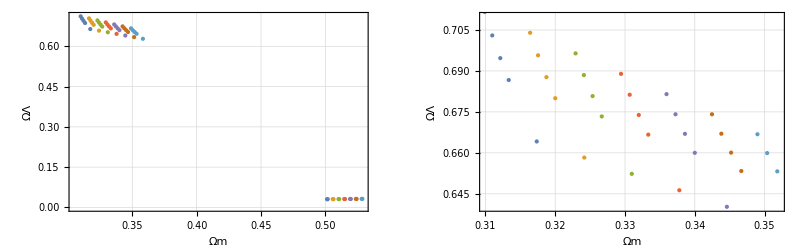

```mathematica
pointsFirst4=SolLabelCDM/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols[[4]] );
pointsLabeled4=SolLabelCDM/. {q_,j_,sols_List}:>({q,j,Ωm,ΩΛ}/. sols[[4]]);
pointsTooltip4=pointsLabeled4/. {q_,j_,xm_,xl_}:>Tooltip[{xm,xl},Row[{"q0 = ",q,", j0 = ",j}]];

p4=ListPlot[pointsTooltip,FrameLabel->{"Ωm","ΩΛ"},PlotStyle->{PointSize[Medium]},Frame->True,GridLines->Automatic];
GraphicsRow[{p4,Show[p4,PlotRange->{{0.31,0.352},{0.64,0.71}}]}]
```

```mathematica
(*Rama 3 de Solucion*)
```

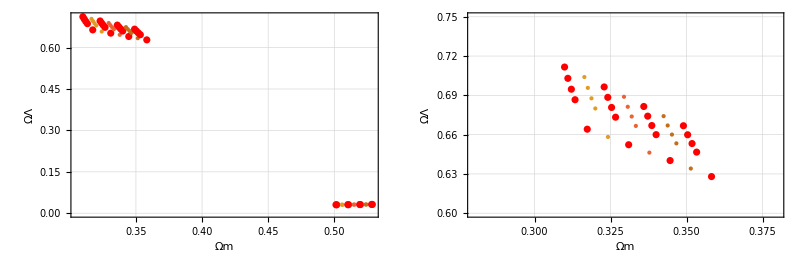

```mathematica
(*Plots de la solucion 3*)
pointsFirst3=SolLabelCDM/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols[[3]] );
pointsLabeled3=SolLabelCDM/. {q_,j_,sols_List}:>({q,j,Ωm,ΩΛ}/. sols[[3]]);
pointsTooltip3=pointsLabeled3/. {q_,j_,xm_,xl_}:>Tooltip[{xm,xl},Row[{"q0 = ",q,", j0 = ",j}]];
p3=ListPlot[pointsTooltip3,FrameLabel->{"Ωm","ΩΛ"},PlotStyle->{Red,PointSize[Medium]},Frame->True,GridLines->Automatic];
GraphicsRow[{p3,Show[p3,PlotRange->{{0.28,0.38},{0.6,0.75}}]},Spacings->0.5]
```

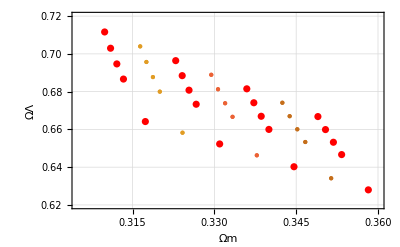

```mathematica
(*Combinación de estos*)
Show[p4,p3,PlotRange->{{0.305,0.36},{0.62,0.72}}]
```

```mathematica
(*Todas las ramas de soluciones*)
```

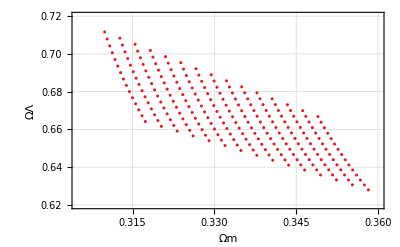

```mathematica
(*Todas las ramas de soluciones*)
pointsCDM=SolLabelCDM/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols);
pointsCDM=Flatten[pointsCDM,2];
AllValuesCDM=ListPlot[pointsCDM,PlotRange->{{0.305,0.36},{0.62,0.72}},PlotStyle->ColorData["Rainbow"]/@Range[Length[pointsCDM]],FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic]
```

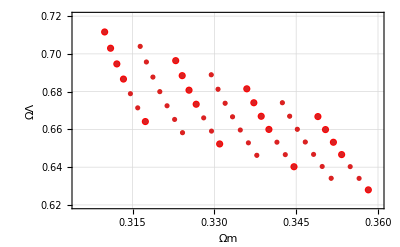

```mathematica
Show[p3,p4,AllValuesCDM,PlotRange->{{0.305,0.36},{0.62,0.72}}]
```

```mathematica
(*Grafico de densidad*)
```

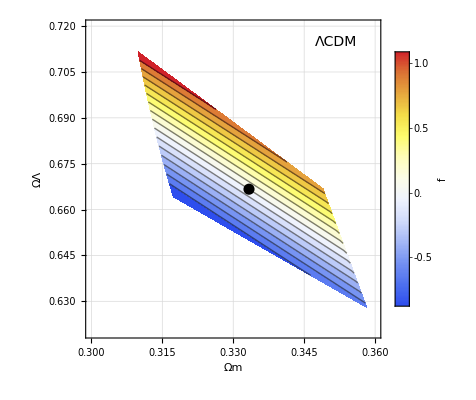

```mathematica
(*Localizacion del punto Central*)
CentralCDM=SolucionCentral[67,-0.5,1];
CentralPointCDM=({Ωm,ΩΛ}/. CentralCDM);

(*Mapa de Color*)
CDMpointsOmegaf=SolLabelCDM/. {q_,j_,sols_List}:>({Ωm,ΩΛ,f}/. sols );
CDMpointsOmegaf=Flatten[CDMpointsOmegaf,2];
pointsCDMFiltered=Select[CDMpointsOmegaf,0.6<=#[[2]]<=0.72&]; (*Un curado filtro de soluciones*)
ListContourPlot[pointsCDMFiltered,Contours->15,ColorFunction->"TemperatureMap",PlotLegends->BarLegend[{"TemperatureMap",MinMax[pointsCDMFiltered[[All,3]]]},LegendLabel->Placed["f",Right]],FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,PlotRange->{{0.3,0.36},{0.62,0.72}},Epilog->{Black,PointSize[0.02],Point[CentralPointCDM],Text[Style["ΛCDM",14],Scaled[{0.85,0.93}]]}]
```

```mathematica
(*Exportando datos en la region de interes*)
Export[FileNameJoin[{NotebookDirectory[],"Data","CDM_rhoNeg_Sigma.csv"}],pointsCDMFiltered]
```

C:\Users\flavi\OneDrive\Escritorio\Research\NMCG\Notebooks\Data\CDM_rhoNeg_Sigma.csv

### CDM2Sigma

```mathematica
SolCDM2Sig=Soluciones[67,-0.50,0.06,1.00,0.06];
CentralCDM=SolucionCentral[67,-0.5,1];
CentralPointCDM=({Ωm,ΩΛ}/. CentralCDM)
```

{{-4.35017,6.63261},{0.656781,0.383812},{0.333333,0.666667},{0.515806,0.0311964}}

```mathematica
(*Todas las ramas de soluciones*)
```

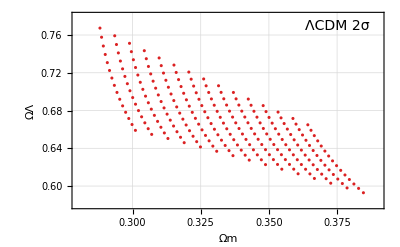

```mathematica
pointsCDM2=SolCDM2Sig/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols);
pointsCDM2=Flatten[pointsCDM2,2];
CDM2Sig=ListPlot[pointsCDM2,PlotRange->{{0.28,0.39},{0.58,0.78}},PlotStyle->ColorData["Rainbow"]/@Range[Length[pointsCDM2]],FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Text[Style["ΛCDM 2σ",14],Scaled[{0.85,0.93}]]}]
```

```mathematica
(*Grafico de densidad*)
```

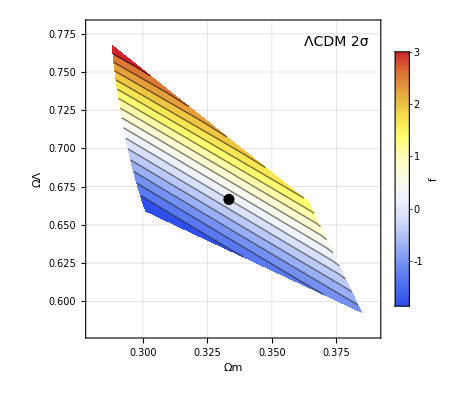

```mathematica
(*Mapa de Color*)
CDMpointsOmegaf2S=SolCDM2Sig/. {q_,j_,sols_List}:>({Ωm,ΩΛ,f}/. sols );
CDMpointsOmegaf2S=Flatten[CDMpointsOmegaf2S,2];
pointsCDMFilt2S=Select[CDMpointsOmegaf2S,0.58<=#[[2]]<=0.77&]; (*Un curado filtro de soluciones*)
ListContourPlot[pointsCDMFilt2S,Contours->15,ColorFunction->"TemperatureMap",PlotLegends->BarLegend[{"TemperatureMap",MinMax[pointsCDMFilt2S[[All,3]]]},LegendLabel->Placed["f",Right]],FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,PlotRange->{{0.28,0.39},{0.58,0.78}},Epilog->{Black,PointSize[0.02],Point[CentralPointCDM],Text[Style["ΛCDM 2σ",14],Scaled[{0.85,0.93}]]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Data","CDM_rhoNeg_2S.csv"}],pointsCDMFilt2S]
```

C:\Users\flavi\OneDrive\Escritorio\Research\NMCG\Notebooks\Data\CDM_rhoNeg_2S.csv

### SLS with 99 Samples: 2403.09910

```mathematica
(*q0 central value is -0.54 ±0.1 and j0 is 0.36±0.52*)
SolLabelSLS=Soluciones[73,-0.54,0.1,0.36,0.52]; 

(*Solución central*)
CentralSLS=SolucionCentral[73,-0.54,0.36];
CentralSLS=Select[CentralSLS,AllTrue[Values[#],Im[#]==0&]&];
CentralPointSLS=({Ωm,ΩΛ}/. CentralSLS);
```

```mathematica
(*Plot de todas las soluciones y la region que nos interesa. PARA TODAS LAS RAMAS DE SOLUCIONES*)
```

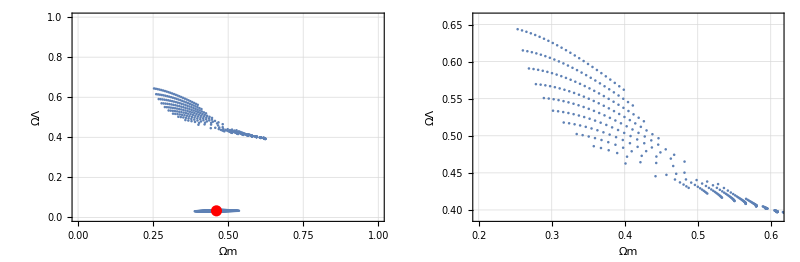

```mathematica
pointsSLS=SolLabelSLS/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols);

pointsSLS=Flatten[pointsSLS,2];

pAll=ListPlot[pointsSLS,PlotRange->{{0,1},{0,1}},FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Red,PointSize[0.02],Point[CentralPointSLS]}];


AllValuesSLS=ListPlot[pointsSLS,PlotRange->{{0.2,0.61},{0.39,0.66}},FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Red,PointSize[0.02],Point[CentralPointSLS]}];


GraphicsRow[{pAll,AllValuesSLS},Spacings->0.5]
```

```mathematica
(*Mapa de regiones, Notar que el valor central está fuera del rango de soluciones físicamente posibles*)
```

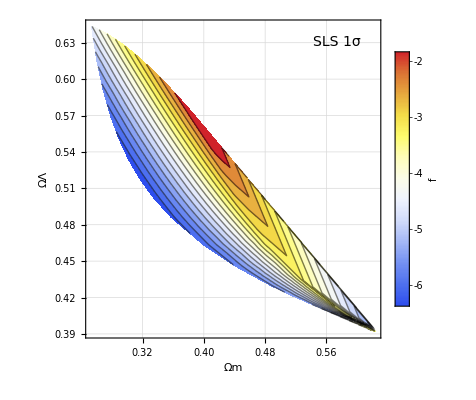

```mathematica
(*Soluciones de la malla*)
SLSpointsOmegaf=SolLabelSLS/. {q_,j_,sols_List}:>({Ωm,ΩΛ,f}/. Select[sols,AllTrue[Values[#],Im[#]==0&]&]);
SLSpointsOmegaf=Flatten[SLSpointsOmegaf,2];
(*Filtro de la región*)
pointsSLSFiltered=Select[SLSpointsOmegaf,0.38<=#[[2]]<=0.67&];
(*Gráfica*)
ListContourPlot[pointsSLSFiltered,Contours->15,ColorFunction->"TemperatureMap",PlotLegends->BarLegend[{"TemperatureMap",MinMax[pointsSLSFiltered[[All,3]]]},LegendLabel->Placed["f",Right]],FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Black,PointSize[0.02],Point[CentralPointSLS],Text[Style["SLS 1σ",14],Scaled[{0.85,0.93}]]}]
```

```mathematica
(*Exportando datos en la region de interes*)
Export[FileNameJoin[{NotebookDirectory[],"Data","SLS_rhoNeg_Sigma_20Samples.csv"}],pointsSLSFiltered]
```

C:\Users\flavi\OneDrive\Escritorio\Research\NMCG\Notebooks\Data\SLS_rhoNeg_Sigma_20Samples.csv

### SLS with 99 Samples 2σ

```mathematica
(*q0 central value is -0.54 ±0.1 and j0 is 0.36±0.52*)
SolSLS2S=Soluciones[73,-0.54,0.2,0.36,1.04]; 

(*Solución central*)
CentralSLS=SolucionCentral[73,-0.54,0.36];
CentralSLS=Select[CentralSLS,AllTrue[Values[#],Im[#]==0&]&];
CentralPointSLS=({Ωm,ΩΛ}/. CentralSLS);
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
pointsSLS2S=SolSLS2S/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols);

pointsSLS2S=Flatten[pointsSLS2S,2];

pAll2S=ListPlot[pointsSLS2S,PlotRange->{{0,1},{0,1}},FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Red,PointSize[0.02],Point[CentralPointSLS]}];


AllValuesSLS2S=ListPlot[pointsSLS2S,PlotRange->{{0.2,0.8},{0.3,0.9}},FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Red,PointSize[0.02],Point[CentralPointSLS]}];


GraphicsRow[{pAll2S,AllValuesSLS2S},Spacings->0.5]
```

-Graphics-

```mathematica
(*Filtro de la región y valores reales*)
SLS2S=SolSLS2S/. {q_,j_,sols_List}:>({Ωm,ΩΛ,f}/. Select[sols,AllTrue[Values[#],Im[#]==0&]&]);
SLS2S=Flatten[SLS2S,2];
SLS2Filtered=Select[SLS2S,0.3<=#[[2]]<=0.95&];
(*Exportando datos en la region de interes*)
Export[FileNameJoin[{NotebookDirectory[],"Data","SLS_rhoNeg_2S.csv"}],SLS2Filtered]
```

C:\Users\flavi\OneDrive\Escritorio\Research\NMCG\Notebooks\Data\SLS_rhoNeg_2S.csv

### Complementar datos por lado izquierdo

```mathematica
SolVals[H0val_,q0c_,eq_,j0c_,ej_,dots_]:=Table[{q,j,SolucionCentral[H0val,q,j]},{q,q0c-eq,q0c+eq,2 eq/(dots-1)},{j,j0c-ej,j0c+ej,2 ej/(dots-1)}]
```

```mathematica
SLS2=Import[FileNameJoin[{NotebookDirectory[],"Data","SLS_rhoNeg_2S.csv"}]];
```

```mathematica
(*-0.54 ±0.1 and j0 is 0.36±0.52*)
q0min=-0.54-0.2
q0max=-0.54+0.2;
j0min=0.36-2*0.52;
j0max=0.36+2*0.52
```

-0.74

1.4

```mathematica
temp3=SolucionCentral[73,q0max,j0max];
temp4=SolucionCentral[73,q0max-0.1,j0max-0.52];
```

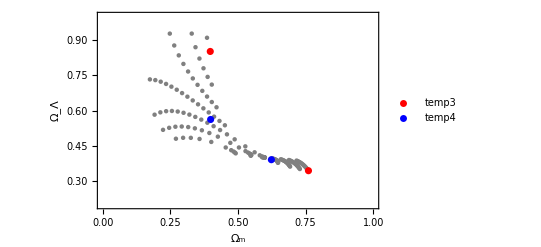

```mathematica
temps={temp3,temp4};

tempPoints=Table[({Ωm,ΩΛ}/. #)&/@temps[[i]],{i,2}];

Show[ListPlot[SLS2[[All,1;;2]],PlotStyle->{Gray,PointSize[0.008]}],ListPlot[tempPoints,PlotStyle->{Red,Blue,Green,Orange},PlotLegends->{"temp3","temp4"}],PlotRange->{{0,1},{0.2,1}},Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(Ω\), \(m\)]\)","\!\(\*SubscriptBox[\(Ω\), \(Λ\)]\)"}]
```

```mathematica
qmean=(q0max+q0max-0.1)/2;
qe=0.04+0.1;
j0mean=(j0max+j0max-0.52)/2;
je=0.2
```

0.2

```mathematica
j0max
```

1.4

```mathematica
j0min
```

-0.68

```mathematica
q0max
```

-0.34

```mathematica
-0.6+(qe+0.2)
```

-0.26

```mathematica
je
```

0.2

```mathematica
(*rango de valores q0 = (-0.74,-0.34), j0=(1.4,-0.68)*)
tempV0=SolVals[73,-0.54,0.2,1.1,0.2,10];
```

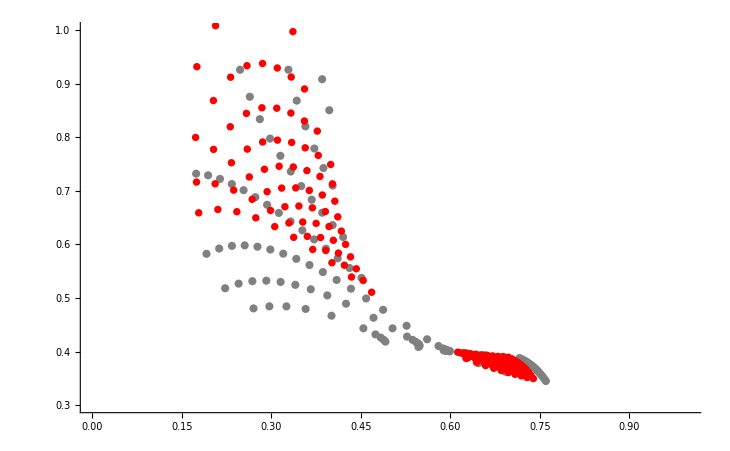

```mathematica
temp0VPoints=tempV0/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols);
temp0VPoints=Flatten[temp0VPoints,2];
tempPlot0=ListPlot[temp0VPoints,PlotRange->{{0,1},{0.3,1}},PlotStyle->Red];
Show[ListPlot[SLS2[[All,1;;2]],PlotStyle->{Gray,PointSize[0.008]}],tempPlot0,PlotRange->{{0,1},{0.3,1}}]
```

```mathematica
0.24742163494962097,0.9092116264455674
```

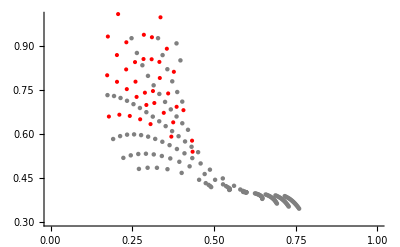

```mathematica
temp0VPointsF=Select[temp0VPoints,Function[p,And[And@@(Im[#]==0&/@p),(p[[1]]!=0.24742163494962097||p[[2]]!=0.9092116264455674),AllTrue[SLS2,Function[q,Abs[p[[1]]-q[[1]]]>10^-1.8||Abs[p[[2]]-q[[2]]]>10^-1.8]]]]];
tempPlot1=ListPlot[temp0VPointsF,PlotRange->{{0,1},{0.3,1}},PlotStyle->Red];
Show[ListPlot[SLS2[[All,1;;2]],PlotStyle->{Gray,PointSize[0.008]}],tempPlot1,PlotRange->{{0,1},{0.3,1}}]
```

```mathematica
SLS2FullPoint=Select[Join[SLS2[[All,1;;2]],temp0VPointsF],#[[2]]<0.93&];

Export[FileNameJoin[{NotebookDirectory[],"Data","SLS_rhoNeg_2S_v2.csv"}],SLS2FullPoint]
```

C:\Users\flavi\OneDrive\Escritorio\Research\NMCG\Notebooks\Data\SLS_rhoNeg_2S_v2.csv

### SLS with 99 Samples, around central Value

```mathematica
SolLabelSLS=Soluciones[73,-0.54,0.01,0.36,0.052]; 
(*Solución central*)
CentralSLS=SolucionCentral[73,-0.54,0.36];
CentralSLS=Select[CentralSLS,AllTrue[Values[#],Im[#]==0&]&];
CentralPointSLS=({Ωm,ΩΛ}/. CentralSLS);
```

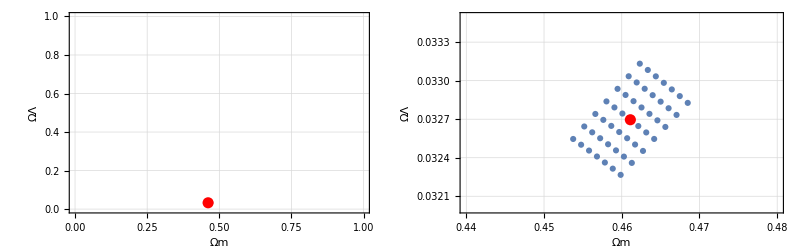

```mathematica
pointsSLS=SolLabelSLS/. {q_,j_,sols_List}:>({Ωm,ΩΛ}/. sols);

pointsSLS=Flatten[pointsSLS,2];

pAll=ListPlot[pointsSLS,PlotRange->{{0,1},{0,1}},FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Red,PointSize[0.02],Point[CentralPointSLS]}];


AllValuesSLS=ListPlot[pointsSLS,PlotRange->{{0.44,0.48},{0.032,0.0335}},FrameLabel->{"Ωm","ΩΛ"},Frame->True,GridLines->Automatic,Epilog->{Red,PointSize[0.02],Point[CentralPointSLS]}];


GraphicsRow[{pAll,AllValuesSLS},Spacings->0.5]
```